```mathematica
arrow[x_]:={{{x,x},{x,f[x]}},{{x,f[x]},{f[x],f[x]}}}
```

```mathematica
f[x_]:=x^0.5
```

```mathematica
myvals=RecurrenceTable[{x[t+1]==x[t]^0.5,x[0]==0.2},x,{t,0,5}]
```

{0.2,0.447214,0.66874,0.817765,0.904304,0.950949}

```mathematica
myvals2=RecurrenceTable[{x[t+1]==x[t]^0.5,x[0]==1.6},x,{t,0,4}]
```

{1.6,1.26491,1.12468,1.06051,1.02981}

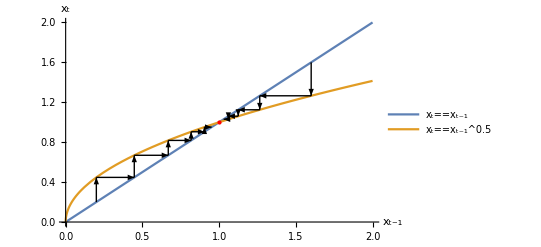

```mathematica
plt=Plot[{x,f[x]},{x,0,2},Epilog-> {{Arrowheads[Small],Arrow[ArrayReshape[arrow/@myvals,{10,2,2}]]},{Arrowheads[Small],Arrow[ArrayReshape[arrow/@myvals2,{8,2,2}]]},{PointSize[Large],Red,Point[{1,1}]}},PlotLegends->{Subscript["x","t"]==Subscript["x","t-1"],Subscript["x","t"]==Subsuperscript["x","t-1","0.5"]},AxesLabel->{Subscript["x","t-1"],Subscript["x","t"]}]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/ramsey/Steady_States.png",plt]
```

/home/eric/eric-roca.github.io/static/img/ramsey/Steady_States.png

```mathematica
Solve[{x==3./10*x+y^(1/2),y==x-1/2*y},{x,y}]
```

{{x→0.,y→0.},{x→1.36054,y→0.907029}}

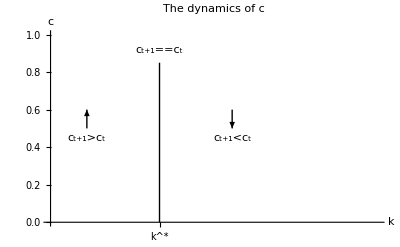

```mathematica
plt2=Plot[{0},{x,0,1},PlotRange->{{0.1,1},{0,1}},AxesLabel->{"k","c"},Epilog->{Text[Subscript["c","t+1"]==Subscript["c","t"],{0.4,0.92}],Line[{{0.4,0},{0.4,0.85}}],{Arrowheads[Small],Arrow[{{0.2,0.5},{0.2,0.6}}]},{Arrowheads[Small],Arrow[{{0.6,0.6},{0.6,0.5}}]},Text[Subscript["c","t+1"]>Subscript["c","t"],{0.2,0.45}],Text[Subscript["c","t+1"]<Subscript["c","t"],{0.6,0.45}]},PlotStyle->{Directive[Opacity[ 0],Black]},Ticks->{{{0.4,Superscript["k","*"]}},{None}},PlotLabel->Style["The dynamics of c",Black,Larger,Bold]]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/ramsey/dynamics_c.png",plt2]
```

/home/eric/eric-roca.github.io/static/img/ramsey/dynamics_c.png

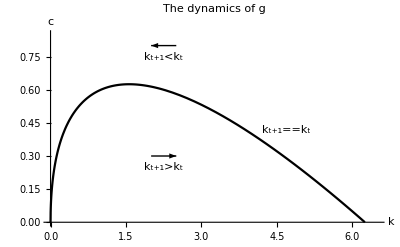

```mathematica
plt3=Plot[x^0.5-0.4*x,{x,0,7},PlotRange->{{0,6.5},{0,0.85}},AxesLabel->{"k","c"},Epilog->{Text[Subscript["k","t+1"]==Subscript["k","t"],{4.2,(#^0.5-0.4#&@4.2)+0.05},Left],{Arrowheads[Small],Arrow[{{2.5,0.8},{2,0.8}}]},{Arrowheads[Small],Arrow[{{2,0.3},{2.5,0.3}}]},Text[Subscript["k","t+1"]>Subscript["k","t"],{2.25,0.25}],Text[Subscript["k","t+1"]<Subscript["k","t"],{2.25,0.75}]},PlotStyle->{Directive[Black]},Ticks->None,PlotLabel->Style["The dynamics of g",Black,Larger,Bold]]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/ramsey/dynamics_g.png",plt3]
```

/home/eric/eric-roca.github.io/static/img/ramsey/dynamics_g.png

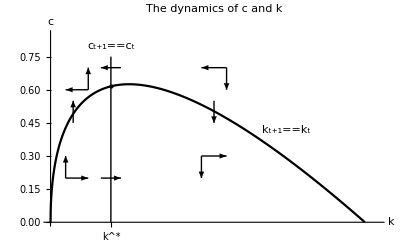

```mathematica
plt4=Plot[x^0.5-0.4*x,{x,0,7},PlotRange->{{0,6.5},{0,0.85}},AxesLabel->{"k","c"},Epilog->{Line[{{1.2,0},{1.2,0.75}}],{PointSize[Large],Point[{1.2,#^0.5-0.4*#&@1.2}]},Text[Subscript["c","t+1"]==Subscript["c","t"],{1.2,0.8}],Text[Subscript["k","t+1"]==Subscript["k","t"],{4.2,(#^0.5-0.4#&@4.2)+0.05},Left],{Arrowheads[Small],{Arrow[{{0.3,0.2},{0.75,0.2}}],Arrow[{{0.3,0.2},{0.3,0.3}}],Arrow[{{0.75,0.6},{0.3,0.6}}],Arrow[{{0.75,0.6},{0.75,0.7}}],Arrow[{{3,0.3},{3.5,0.3}}],Arrow[{{3,0.3},{3,0.2}}],Arrow[{{3.5,0.7},{3,0.7}}],Arrow[{{3.5,0.7},{3.5,0.6}}],Arrow[{{1,0.2},{1.4,0.2}}],Arrow[{{1.4,0.7},{1,0.7}}],Arrow[{{0.45,0.45},{0.45,0.55}}],Arrow[{{3.25,0.55},{3.25,0.45}}]}}},PlotStyle->{Directive[Black]},Ticks->{{{1.2,Superscript["k","*"]}},{None}},PlotLabel->Style["The dynamics of c and k",Black,Larger,Bold]]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/ramsey/phase_diagram.png",plt4]
```

/home/eric/eric-roca.github.io/static/img/ramsey/phase_diagram.png

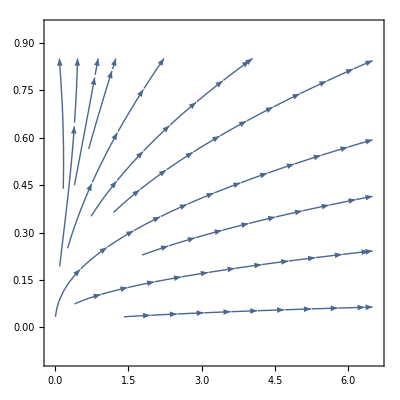

```mathematica
StreamPlot[{k^0.5+(1-0.4)*k-c,5/9*(0.5*k^(-0.5)+1-0.4)*c},{k,0.01,6.5},{c,0,0.85}]
```

```mathematica
myR[k0_,c0_]:=(tmp=RecurrenceTable[{k[t+1]==k[t]^0.5+(1-0.4)*k[t]-c[t],c[t+1]==0.946579*(0.5*k[t+1]^(-0.5)+1-0.4)*c[t],k[0]==k0,c[0]==c0},{k[t],c[t]},{t,0,20}];tmp=Select[tmp,Element[#[[1]],Reals]&&Element[#[[2]],Reals]&];ArrayReshape[Table[{{#[[i]]},{#[[i+1]]}},{i,1,Length[tmp]-1}]&@tmp,{Length[tmp]-1,2,2}])
```

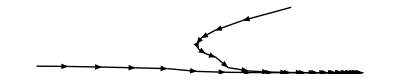

```mathematica
Graphics[Arrow[#]&/@{myR[5,1],myR[1,0.1]}]
```

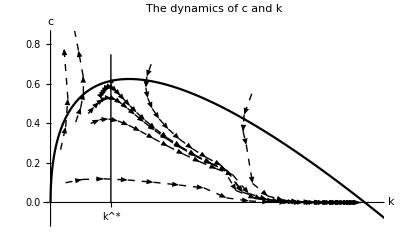

```mathematica
Plot[x^0.5-0.4*x,{x,0,7},PlotRange->{{0,6.5},{-0.1,0.85}},AxesLabel->{"k","c"},Epilog->{Line[{{1.2,0},{1.2,0.75}}],{PointSize[Large],Point[{1.2,#^0.5-0.4*#&@1.2}]},{Arrowheads[Small],Dashed,Arrow[#]&/@{myR[1,0.6-0.055],myR[0.75,0.45],myR[4,0.55],myR[2,0.7],myR[0.8,0.4],myR[0.3,0.1],myR[0.5,0.5^0.5-0.4*0.5-0.1],myR[0.2,0.2^0.5-0.4*0.2-0.1]}}},PlotStyle->{Directive[Black]},Ticks->{{{1.2,Superscript["k","*"]}},{None}},PlotLabel->Style["The dynamics of c and k",Black,Larger,Bold]]
```